### Start choosing the example:

```mathematica
t=7;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->5,U2->5}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.056553 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.08008,Null}

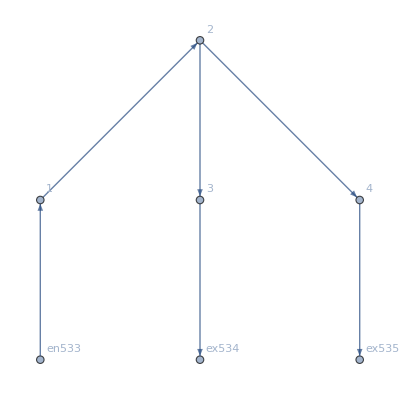

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→8.,u561→6.,u562→6.,u563→5.,u564→5.,u565→8.,u566→6.,u567→5.,u568→5.,u569→5.,u570→5.,u571→8.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→6.75229,u561→5.70576,u562→5.70576,u563→5.,u564→5.,u565→6.75229,u566→5.70576,u567→5.,u568→5.,u569→5.,u570→5.,u571→6.75229|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→6.82592,u561→5.72685,u562→5.72685,u563→5.,u564→5.,u565→6.82592,u566→5.72685,u567→5.,u568→5.,u569→5.,u570→5.,u571→6.82592|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.01949×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.01949×10^-16

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→6.99482,u561→5.77321,u562→5.77321,u563→5.,u564→5.,u565→6.99482,u566→5.77321,u567→5.,u568→5.,u569→5.,u570→5.,u571→6.99482|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.67112×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.67112×10^-16

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→7.79269,u561→5.9592,u562→5.9592,u563→5.,u564→5.,u565→7.79269,u566→5.9592,u567→5.,u568→5.,u569→5.,u570→5.,u571→7.79269|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.71948×10^-15,ComplexInfinity]

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→8.,u561→6.,u562→6.,u563→5.,u564→5.,u565→8.,u566→6.,u567→5.,u568→5.,u569→5.,u570→5.,u571→8.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.28037×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.47288×10^-15

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→8.53675,u561→6.0941,u562→6.0941,u563→5.,u564→5.,u565→8.53675,u566→6.0941,u567→5.,u568→5.,u569→5.,u570→5.,u571→8.53675|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.19874×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.19874×10^-16

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→9.92172,u561→6.27899,u562→6.27899,u563→5.,u564→5.,u565→9.92172,u566→6.27899,u567→5.,u568→5.,u569→5.,u570→5.,u571→9.92172|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.7184×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.39569×10^-16

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→10.7031,u561→6.35738,u562→6.35738,u563→5.,u564→5.,u565→10.7031,u566→6.35738,u567→5.,u568→5.,u569→5.,u570→5.,u571→10.7031|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.24322×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.24322×10^-16

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→13.5434,u561→6.55247,u562→6.55247,u563→5.,u564→5.,u565→13.5434,u566→6.55247,u567→5.,u568→5.,u569→5.,u570→5.,u571→13.5434|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.12658×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.29894×10^-16

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→16.5708,u561→6.6767,u562→6.6767,u563→5.,u564→5.,u565→16.5708,u566→6.6767,u567→5.,u568→5.,u569→5.,u570→5.,u571→16.5708|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.17756×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.17756×10^-17

<|j536→2.,j537→1.,j538→1.,j539→1.,j540→1.,j541→2.,j542→0.,j543→0.,j544→0.,j545→0.,j546→0.,j547→0.,jt548→0.,jt549→2.,jt550→1.,jt551→1.,jt552→0.,jt553→0.,jt554→0.,jt555→0.,jt556→1.,jt557→0.,jt558→1.,jt559→0.,u560→23.1999,u561→6.82668,u562→6.82668,u563→5.,u564→5.,u565→23.1999,u566→6.82668,u567→5.,u568→5.,u569→5.,u570→5.,u571→23.1999|>